## General

### Initialization

```mathematica
Off[ClebschGordan::"phy"]
Off[ClebschGordan::tri]
Off[SixJSymbol::tri]
Off[General::"spell1"]
Off[General::"spell"]
<<"ErrorBarPlots`";
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Constants

```mathematica
IINa23=3/2;         
IIK39=3/2;
IIK40=4;
IIK41=3/2;
SSNa23=1/2;
SSK39=1/2;
SSK40=1/2;
SSK41=1/2;
```

```mathematica
(* From NIST site or Arimondo: *)
```

```mathematica
AhfNa23=885.8130644*10^6;
AhfK39=230.859860*10^6;
AhfK40=-285.7308*10^6;          
AhfK41=127.0069352*10^6;
```

```mathematica
gS=2.0023193043622;       
gINa23=-0.0008046108; 
gIK39=-0.00014193489; 
gIK40=+0.000176490;
gIK41=-0.00007790600;
```

```mathematica
mNa23=22.98976967;              
mK39=38.9637069;                   
mK40=39.96399867;                   
mK41=40.96182597;
```

```mathematica
c = 299792458;
h=6.62606896*10^-34; 
ℏ=h/(2π);
muB=9.27400915*10^-24;
a0SI=5.2917720859*10^-11;
a0=1;
hbar=1;
kB=1.3806504*10^-23;  
me=9.10938215*10^-31;
u=1.660538782*10^-27;                   (*NIST site*)
```

```mathematica
Eh=4.35974394*10^-18;
```

```mathematica
deltaB=5;
minBPlot=0;
maxBPlot=1200;
highBLimit=1000;
```

## Choice of species

```mathematica
SS1=SSNa23;
SS2=SSK40;
II1=IINa23;
II2=IIK40;
Ahf1=AhfNa23;
Ahf2=AhfK40;
gI1=gINa23;
gI2=gIK40;
```

```mathematica
μ=(mNa23*mK40)/(mNa23+mK40)*u
```

2.42343×10^-26

```mathematica
DeX = 5273.6157; (*Our measured value*)
De0 = 5212.0447; (*Our measured value*)
De0FB=5211.98248; (*Our truly measured photon difference*)
X00=61.571009321984796; (*X00 Ground state energy = zero point energy of ground state potential*)
FB0=-1.865; (*FB bound state hyperfine energy, with respect to hyperfine center of mass, in GHz*)
```

## Parameters of B-c-b manifold

### 804nm:

```mathematica
FoundLines={c/372.61850  10^-3,c/372.61051  10^-3,c/372.59660 10^-3,c/372.59100 10^-3,c/372.55400 10^-3,c/372.55920 10^-3};
WavenumberFoundLinesAbs=Sort[1/FoundLines/10^-9/100+De0FB+X00];
FoundLinesList=Table[{-1,WavenumberFoundLinesAbs[[v]]},{v,1,Length[WavenumberFoundLinesAbs]}];
B1J1 = 17701.534165517216;
B1J2 = 17701.757314569702;
c3N1J0=17702.50561544268;
B0c =0.03980720445338193;
B1Pi =17701.478378254094;
BvB1Pi =0.055787263122084596;
c3 =17701.35467879664;
Bvc3 = 0.03980886080387336;
b3Pi =17710.71202147651;
Bvb3Pi = 0.05489108563801892;
γ0 = 0.0124;
λ0 = 0.6;
ξBc0 = 0.582;
ξbc0 = 2;
BL0 =0.0035;
A=15.557 -0.0112(66+1/2) ;(* from Amanda Ross, Enfantin, Laser-induced fluorescence of NaK:the b(1) 3Π state, 1986 J.Phys.B:At.Mol.Phys.19 1449
(http://iopscience.iop.org/0022-3700/19/10/014) *)
K1Kowalczyk = 0.0115; (*J.Chem.Phys.91,2779 (1989);doi:10.1063/1.456947*)
```

### 832nm:

```mathematica
(*B1Pi =17289.253;
BvB1Pi =0.06686421440207369;
c3 =17288.328; (*from Dunham with mass-scaling from Ferber 2000 *)
Bvc3 = 0.046723238763320296
b3Pi = 17301.87; (*from Kowalczyk 1989 applying the isotopic shift from Dunham coefficients in my file*)
Bvb3Pi = 0.0633547;
γ = 0.0024; (*Kowalczyk*)
λ0 = 0.07; (* Kowalczyk, Forbidden transitions in NaK, 1989 *)
ξBc0 = 0.16;
ξbc0 = 0.7657670034690864 (* From FCF and Ferber paper *);
BL0 =0.0035;
A=15.557 -0.0112(59+1/2);*)
K1Kowalczyk = 0.0104; (*J.Chem.Phys.91,2779 (1989);doi:10.1063/1.456947*)(*Same as Kato!*)
```

```mathematica
(*Chop[Sort[Transpose[Eigensystem[HmatrixJ1[-0.1,1.47,-0.21,0.158,0.07,0.9,0]]]][[All,1]],10^-3]*)
```

```mathematica
Bf0=85.7; (*Bfield in G*)
K1=Ahf1/c/100*0.84^2/2;
K2 = Ahf2/c/100*0.39^2/2; (*Kato*)
```

## Molecular Basis Set

```mathematica
maxN=1;
J=1;
maxTotalMF = J+II1+II2;
```

### 3Σ+

c3state: |S=1,Λ=0,N=J-1,J,J+1,J,M,I1,MI1,I2,MI2>

```mathematica
c3basis=Table[{},{i,2*maxTotalMF+1}];
For[Np=1,Np≤maxN,
For[M=-J,M≤J,
For[MI1=-II1,MI1≤ II1,
For[MI2=-II2,MI2≤II2,
MF=M+MI1+MI2;
(*Print["J: ",J, " MJ: ", M, " MI1: ", MI1, " MF1: ",MF1," entry: ",maxTotalMF+MF1+1];*)
AppendTo[c3basis[[maxTotalMF+MF+1]],{1,0,Np,J,M,MI1,MI2}];
MI2++];
MI1++];
M++];
Np+=2];
nc3States=Table[0,{i,2*maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nc3States[[i]] = Length[c3basis[[i]]];
i++];
c3basis[[4]]//MatrixForm
```

(1 | 0 | 1 | 1 | -1 | -3/2 | -1
1 | 0 | 1 | 1 | -1 | -1/2 | -2
1 | 0 | 1 | 1 | -1 | 1/2 | -3
1 | 0 | 1 | 1 | -1 | 3/2 | -4
1 | 0 | 1 | 1 | 0 | -3/2 | -2
1 | 0 | 1 | 1 | 0 | -1/2 | -3
1 | 0 | 1 | 1 | 0 | 1/2 | -4
1 | 0 | 1 | 1 | 1 | -3/2 | -3
1 | 0 | 1 | 1 | 1 | -1/2 | -4)

```mathematica
Total[nc3States]
```

108

```mathematica
2*5*4*9
```

360

```mathematica
c3F1mF1basis=Table[{},{i,2*maxTotalMF+1}];
For[Np=1,Np≤maxN,
For[F=Abs[J-II1],F≤J+II1,
For[MF1=-F,MF1≤F,
For[MI2=-II2,MI2≤II2,
AppendTo[c3F1mF1basis[[maxTotalMF+MF1+MI2+1]],{1,0,Np,J,F,MF1,MI2}];
MI2++];
MF1++];
F++];
Np+=2];
nc3F1mF1States=Table[0,{i,2* maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nc3F1mF1States[[i]] = Length[c3F1mF1basis[[i]]];
i++];
```

```mathematica
Total[nc3F1mF1States]
```

108

```mathematica
c3F1mF1basis[[8]]//MatrixForm
```

(1 | 0 | 1 | 1 | 1/2 | -1/2 | 1
1 | 0 | 1 | 1 | 1/2 | 1/2 | 0
1 | 0 | 1 | 1 | 3/2 | -3/2 | 2
1 | 0 | 1 | 1 | 3/2 | -1/2 | 1
1 | 0 | 1 | 1 | 3/2 | 1/2 | 0
1 | 0 | 1 | 1 | 3/2 | 3/2 | -1
1 | 0 | 1 | 1 | 5/2 | -5/2 | 3
1 | 0 | 1 | 1 | 5/2 | -3/2 | 2
1 | 0 | 1 | 1 | 5/2 | -1/2 | 1
1 | 0 | 1 | 1 | 5/2 | 1/2 | 0
1 | 0 | 1 | 1 | 5/2 | 3/2 | -1
1 | 0 | 1 | 1 | 5/2 | 5/2 | -2)

```mathematica
ClebschMatrixF1=Table[{},{i,2*maxTotalMF+1}];
For[iMF=1,iMF≤2*maxTotalMF+1,
ClebschMatrixF1[[iMF]]=Table[Module[{Nl,J,M,MI1,Nr,Jr,F,MF,MI2},
{Nr,Jr,F,MF,MI2r}=c3F1mF1basis[[iMF,i,3;;7]];
{Nl,J,M,MI1,MI2l}=c3basis[[iMF,j,3;;7]];
KroneckerDelta[J,Jr]KroneckerDelta[Nl,Nr]KroneckerDelta[MI2l,MI2r]ClebschGordan[{J,M},{II1,MI1},{F,MF}]],{i,1,nc3F1mF1States[[iMF]]},{j,1,nc3States[[iMF]]}];
iMF++];
```

```mathematica
Table[Sum[ClebschMatrixF1[[7,i,j]]^2,{i,1,nc3F1mF1States[[7]]}],{j,1,nc3States[[7]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ClebschMatrixF1[[7]]
```

{{0,0,1/(√6),0,0,-1/(√3),0,0,1/(√2),0,0,0},{0,0,0,1/(√2),0,0,-1/(√3),0,0,1/(√6),0,0},{0,-√(2/5),0,0,√(3/5),0,0,0,0,0,0,0},{0,0,-2 √(2/15),0,0,1/(√15),0,0,√(2/5),0,0,0},{0,0,0,-√(2/5),0,0,-1/(√15),0,0,2 √(2/15),0,0},{0,0,0,0,0,0,0,-√(3/5),0,0,√(2/5),0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,√(3/5),0,0,√(2/5),0,0,0,0,0,0,0},{0,0,√(3/10),0,0,√(3/5),0,0,1/(√10),0,0,0},{0,0,0,1/(√10),0,0,√(3/5),0,0,√(3/10),0,0},{0,0,0,0,0,0,0,√(2/5),0,0,√(3/5),0},{0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
F1Projector[iMF_,F1_]:=ClebschMatrixF1[[iMF]]ᵀ.DiagonalMatrix[Table[KroneckerDelta[c3F1mF1basis[[iMF,i,5]],F1],{i,1,nc3F1mF1States[[iMF]]}]].ClebschMatrixF1[[iMF]];
```

```mathematica
c3F2mF2basis=Table[{},{i,2*maxTotalMF+1}];
For[Np=1,Np≤maxN,
For[F2=Abs[J-II2],F2≤J+II2,
For[MI1=-II1,MI1≤II1,
For[MF2=-F2,MF2≤F2,
AppendTo[c3F2mF2basis[[maxTotalMF+MI1+MF2+1]],{1,0,Np,J,F2,MI1,MF2}];
MF2++];
MI1++];
F2++];
Np+=2];
nc3F2mF2States=Table[0,{i,2* maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nc3F2mF2States[[i]] = Length[c3F2mF2basis[[i]]];
i++];
```

```mathematica
Total[nc3F2mF2States]
```

108

```mathematica
c3F2mF2basis[[8]]//MatrixForm
```

(1 | 0 | 1 | 1 | 3 | -3/2 | 2
1 | 0 | 1 | 1 | 3 | -1/2 | 1
1 | 0 | 1 | 1 | 3 | 1/2 | 0
1 | 0 | 1 | 1 | 3 | 3/2 | -1
1 | 0 | 1 | 1 | 4 | -3/2 | 2
1 | 0 | 1 | 1 | 4 | -1/2 | 1
1 | 0 | 1 | 1 | 4 | 1/2 | 0
1 | 0 | 1 | 1 | 4 | 3/2 | -1
1 | 0 | 1 | 1 | 5 | -3/2 | 2
1 | 0 | 1 | 1 | 5 | -1/2 | 1
1 | 0 | 1 | 1 | 5 | 1/2 | 0
1 | 0 | 1 | 1 | 5 | 3/2 | -1)

```mathematica
ClebschMatrixF2=Table[{},{i,2*maxTotalMF+1}];
For[iMF=1,iMF≤2*maxTotalMF+1,
ClebschMatrixF2[[iMF]]=Table[Module[{Nl,J,M,MI1l,MI2,Nr,Jr,F2,MI1r,MF2},
{Nr,Jr,F2,MI1r,MF2}=c3F2mF2basis[[iMF,i,3;;7]];
{Nl,J,M,MI1l,MI2}=c3basis[[iMF,j,3;;7]];
KroneckerDelta[J,Jr]KroneckerDelta[Nl,Nr]KroneckerDelta[MI1l,MI1r]ClebschGordan[{J,M},{II2,MI2},{F2,MF2}]],{i,1,nc3F2mF2States[[iMF]]},{j,1,nc3States[[iMF]]}];
iMF++];
```

```mathematica
Table[Sum[ClebschMatrixF2[[7,i,j]]^2,{i,1,nc3F2mF2States[[7]]}],{j,1,nc3States[[7]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ClebschMatrixF2[[7]]//MatrixForm;
```

### B1Π

B1Pi state: |S=0,Λ=1,N=J,J,M,I1,MI1,I2,MI2>

```mathematica
B1basis=Table[{},{i,2*maxTotalMF+1}];
For[M=-J,M≤J,
For[MI1=-II1,MI1≤II1,
For[MI2=-II2,MI2≤II2,
MF=M+MI1+MI2;
AppendTo[B1basis[[maxTotalMF+MF+1]],{0,1,J,J,M,MI1,MI2}];
MI2++];
MI1++];
M++];
nB1States = Table[0,{i,2*maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nB1States[[i]]=Length[B1basis[[i]]];
i++];
nB1States[[maxTotalMF+3/2+1]]//MatrixForm
B1basis[[maxTotalMF+3/2+1]]//MatrixForm;
```

12

b3Pi state: |S=1,Λ=1,Ω,J,M,I1,MI1,I2,MI2>

Note: Only the “-“ parity is required, as we start with positive parity in the FB state (and want to end up in positive parity in the absolute ground state). The proper parity states are superpositions of |Ω> - (-1)^(J-S)|-Ω>. These are alternating e-f states.

### b3Π

```mathematica
b3basis=Table[{},{i,2*maxTotalMF+1}];
For[Ω=0,Ω≤1,
For[M=-J,M≤J,
For[MI1=-II1,MI1≤II1,
For[MI2=-II2,MI2≤II2,
MF=M+MI1+MI2;
AppendTo[b3basis[[maxTotalMF+MF+1]],{1,1,Ω,J,M,MI1,MI2}];
MI2++];
MI1++];
M++];
Ω++];
nb3States=Table[0,{i,2*maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nb3States[[i]]=Length[b3basis[[i]]];
i++];
nb3States//MatrixForm;
b3basis[[4]]//MatrixForm
```

(1 | 1 | 0 | 1 | -1 | -3/2 | -1
1 | 1 | 0 | 1 | -1 | -1/2 | -2
1 | 1 | 0 | 1 | -1 | 1/2 | -3
1 | 1 | 0 | 1 | -1 | 3/2 | -4
1 | 1 | 0 | 1 | 0 | -3/2 | -2
1 | 1 | 0 | 1 | 0 | -1/2 | -3
1 | 1 | 0 | 1 | 0 | 1/2 | -4
1 | 1 | 0 | 1 | 1 | -3/2 | -3
1 | 1 | 0 | 1 | 1 | -1/2 | -4
1 | 1 | 1 | 1 | -1 | -3/2 | -1
1 | 1 | 1 | 1 | -1 | -1/2 | -2
1 | 1 | 1 | 1 | -1 | 1/2 | -3
1 | 1 | 1 | 1 | -1 | 3/2 | -4
1 | 1 | 1 | 1 | 0 | -3/2 | -2
1 | 1 | 1 | 1 | 0 | -1/2 | -3
1 | 1 | 1 | 1 | 0 | 1/2 | -4
1 | 1 | 1 | 1 | 1 | -3/2 | -3
1 | 1 | 1 | 1 | 1 | -1/2 | -4)

```mathematica
Total[nb3States]
```

216

```mathematica
Fullbasis=Table[{},{i,2 maxTotalMF+1}];
nStates=Table[0,{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
Fullbasis[[iMF]] = Join[B1basis[[iMF]],c3basis[[iMF]],b3basis[[iMF]]];
nStates[[iMF]]=Length[Fullbasis[[iMF]]];
iMF++];
Fullbasis[[2]]//MatrixForm
```

(0 | 1 | 1 | 1 | -1 | -3/2 | -3
0 | 1 | 1 | 1 | -1 | -1/2 | -4
0 | 1 | 1 | 1 | 0 | -3/2 | -4
1 | 0 | 1 | 1 | -1 | -3/2 | -3
1 | 0 | 1 | 1 | -1 | -1/2 | -4
1 | 0 | 1 | 1 | 0 | -3/2 | -4
1 | 1 | 0 | 1 | -1 | -3/2 | -3
1 | 1 | 0 | 1 | -1 | -1/2 | -4
1 | 1 | 0 | 1 | 0 | -3/2 | -4
1 | 1 | 1 | 1 | -1 | -3/2 | -3
1 | 1 | 1 | 1 | -1 | -1/2 | -4
1 | 1 | 1 | 1 | 0 | -3/2 | -4)

```mathematica
nStates
```

{4,12,24,36,44,48,48,48,48,44,36,24,12,4}

```mathematica
Projector[iMF_,J_]:=DiagonalMatrix[Table[KroneckerDelta[Fullbasis[[iMF,i,4]],J],{i,1,nStates[[iMF]]}]];
B1PiProjector[iMF_]:=DiagonalMatrix[Table[KroneckerDelta[Fullbasis[[iMF,i,1]],0],{i,1,nStates[[iMF]]}]];
c3Projector[iMF_]:=DiagonalMatrix[Table[KroneckerDelta[Fullbasis[[iMF,i,1]],1]KroneckerDelta[Fullbasis[[iMF,i,2]],0],{i,1,nStates[[iMF]]}]];
b3Projector[iMF_]:=DiagonalMatrix[Table[KroneckerDelta[Fullbasis[[iMF,i,1]],1]KroneckerDelta[Fullbasis[[iMF,i,2]],1],{i,1,nStates[[iMF]]}]];
```

```mathematica
c3Projector[8]//MatrixForm;
```

```mathematica
Projector[8,1]//MatrixForm;
```

```mathematica
c3FmFbasis=Table[{},{i,2*maxTotalMF+1}];
For[Np=1,Np≤maxN,
For[II=Abs[II2-II1],II≤II1+II2,
For[F=Abs[J-II],F≤J+II,
For[MF=-F,MF≤F,
AppendTo[c3FmFbasis[[maxTotalMF+MF+1]],{1,0,Np,J,II,F,MF}];
MF++];
F++];
II++];
Np+=2];
nc3FmFStates=Table[0,{i,2* maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nc3FmFStates[[i]] = Length[c3FmFbasis[[i]]];
i++];
```

```mathematica
c3FmFbasis[[4]]//MatrixForm
```

(1 | 0 | 1 | 1 | 5/2 | 7/2 | -7/2
1 | 0 | 1 | 1 | 7/2 | 7/2 | -7/2
1 | 0 | 1 | 1 | 7/2 | 9/2 | -7/2
1 | 0 | 1 | 1 | 9/2 | 7/2 | -7/2
1 | 0 | 1 | 1 | 9/2 | 9/2 | -7/2
1 | 0 | 1 | 1 | 9/2 | 11/2 | -7/2
1 | 0 | 1 | 1 | 11/2 | 9/2 | -7/2
1 | 0 | 1 | 1 | 11/2 | 11/2 | -7/2
1 | 0 | 1 | 1 | 11/2 | 13/2 | -7/2)

```mathematica
ClebschMatrixF=Table[{},{i,2*maxTotalMF+1}];
For[iMF=1,iMF≤2*maxTotalMF+1,
ClebschMatrixF[[iMF]]=Table[Module[{Nl,J,M,MI1,MI2,Nr,Jr,II,F,MF},
{Nr,Jr,II,F,MF}=c3FmFbasis[[iMF,i,3;;7]];
{Nl,J,M,MI1,MI2}=c3basis[[iMF,j,3;;7]];
KroneckerDelta[J,Jr]KroneckerDelta[Nl,Nr]ClebschGordan[{II1,MI1},{II2,MI2},{II,MI1+MI2}]ClebschGordan[{J,M},{II,MI1+MI2},{F,MF}]],{i,1,nc3FmFStates[[iMF]]},{j,1,nc3States[[iMF]]}];
iMF++];
```

```mathematica
Table[Sum[ClebschMatrixF[[7,i,j]]^2,{i,1,nc3FmFStates[[7]]}],{j,1,nc3States[[7]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
FProjector[iMF_,F_]:=ClebschMatrixF[[iMF]]ᵀ.DiagonalMatrix[Table[KroneckerDelta[c3FmFbasis[[iMF,i,6]],F],{i,1,nc3FmFStates[[iMF]]}]].ClebschMatrixF[[iMF]];
```

```mathematica
FProjector[4,7/2]//MatrixForm
```

(2/33 | -(2 √6)/55 | (√21)/55 | (4 √(2/7))/45-(√(7/2))/495-1/(3 √14) | -4/55 | (√42)/55 | -(4 √(7/3))/55 | (√7)/55 | -(2 √(14/3))/55
-(2 √6)/55 | 26/165 | -(44 √(2/7))/405+(13 √(7/2))/8910-1/(2 √14) | (16 √(7/3))/165 | (√(2/3))/11 | -(28 √7)/495 | (26 √14)/495 | -(√(14/3))/165 | (4 √7)/495
(√21)/55 | -(44 √(2/7))/405+(13 √(7/2))/8910-1/(2 √14) | 148/495 | -(8 √6)/55 | -(2 √(7/3))/165 | (3 √2)/55 | -16/99 | -13/(165 √3) | (26 √2)/495
(4 √(2/7))/45-(√(7/2))/495-1/(3 √14) | (16 √(7/3))/165 | -(8 √6)/55 | 8/11 | -(2 √14)/165 | 32/(165 √3) | -(4 √6)/55 | -(2 √2)/165 | 8/(165 √3)
-4/55 | (√(2/3))/11 | -(2 √(7/3))/165 | -(2 √14)/165 | 7/55 | -(13 √(14/3))/165 | (2 √(7/3))/33 | -(8 √7)/165 | (16 √(14/3))/165
(√42)/55 | -(28 √7)/495 | (3 √2)/55 | 32/(165 √3) | -(13 √(14/3))/165 | 142/495 | -(34 √2)/165 | (4 √(2/3))/33 | -16/99
-(4 √(7/3))/55 | (26 √14)/495 | -16/99 | -(4 √6)/55 | (2 √(7/3))/33 | -(34 √2)/165 | 268/495 | 32/(165 √3) | -(64 √2)/495
(√7)/55 | -(√(14/3))/165 | -13/(165 √3) | -(2 √2)/165 | -(8 √7)/165 | (4 √(2/3))/33 | 32/(165 √3) | 12/55 | -(8 √6)/55
-(2 √(14/3))/55 | (4 √7)/495 | (26 √2)/495 | 8/(165 √3) | (16 √(14/3))/165 | -16/99 | -(64 √2)/495 | -(8 √6)/55 | 32/55)

## Define initial and final states

```mathematica
Feshbachbasis={{1,0,1,1,-1,-3/2,-1},{1,0,1,1,-1,-1/2,-2},{1,0,1,1,-1,1/2,-3},{1,0,1,1,-1,3/2,-4},{1,0,1,1,0,-3/2,-2},{1,0,1,1,0,-1/2,-3},{1,0,1,1,0,1/2,-4},{1,0,1,1,1,-3/2,-3},{1,0,1,1,1,-1/2,-4}};
Feshbachstates=9;
FBStatecorig=Flatten[({{0.08240952876145596}, {-0.17711918880970354}, {-0.18371836528726135}, {0.1884443089301953}, {0.11010099178052997}, {0.20037961107161398}, {0.6346652181707619}, {-0.31844937434049203}, {-0.5797323581747406}})];
Closedstate = Flatten[({{0.13057109063729425}, {-0.3834006104842659}, {0.08937664152387109}, {0.147683444726944}, {0.14978004817924195}, {0.32525028136954887}, {0.449822808977456}, {-0.6370698332296769}, {-0.2593173420764999}})];(*Closedstate*)Closedstate=Closedstate/(√(Closedstate.Closedstate));
Closedstate2=Flatten[({{0.05671549681666396}, {-0.22743536654910398}, {0.3683135765408059}, {-0.1872375978331425}, {0.06315244388655704}, {0.15994086111366124}, {-0.5678987294260737}, {-0.3664398506058125}, {0.5342665741448438}})];(*Closedstate*)Closedstate2=Closedstate2/(√(Closedstate2.Closedstate2));
Entrancestate = Flatten[({{0}, {0}, {0}, {0.8921009259737215}, {0}, {0}, {-0.3194964302436168}, {0}, {0}})];(*Entrancechannel*)Entrancestate=Entrancestate/(√(Entrancestate.Entrancestate));
OpenState=Flatten[({{-0.00475207112435283}, {0.04166742820798697}, {-0.22085452093184949}, {0.8852371364283604}, {-0.025617339045384258}, {0.1258496472778887}, {-0.3619122184584722}, {-0.042272059753619605}, {0.1080552802039234}})];(*OpenChannel*)OpenState=OpenState/(√(OpenState.OpenState));
(*Channel2=tmat1.tmat.Sum[(HPQPQ[[1,j]]/h/10^9)/(-0.00008-HPQPQ[[j,j]]/h/10^9)UnitVector[12,j],{j,2,12}];
Channel2r=Flatten[{Channel2[[9;;12]],Channel2[[6;;8]],Channel2[[4;;5]]}];FBStatec=Channel2r;FBStatec=FBStatec/(√(FBStatec.FBStatec));*)
WeightedABMQstates={-0.09591789617660976,0.2381681958830213,0.10188612874987854,-0.18375617717015189,-0.11242950267393496,-0.22715963923907875,-0.6442365509439552,0.40251150274264713,0.49862853267739377};
(*Channel2=tmat1.tmat.UnitVector[12,1];Channel2r=Flatten[{Channel2[[9;;12]],Channel2[[6;;8]],Channel2[[4;;5]]}]; Channel2r=Channel2r/(√(Channel2r.Channel2r));*)
PChannelABM ={0.,0.,0.,0.9414444000098469,0.,0.,-0.3371682691032764,0.,0.};
FBStatec=√α WeightedABMQstates+√(1-α)PChannelABM /.α->.8165;FBStatec=FBStatec/(√(FBStatec.FBStatec));
FBStatec.FBStatec
```

1.

```mathematica
{FBStatec//MatrixForm,Feshbachbasis//MatrixForm}
```

{(-0.0852253
0.211618
0.0905282
0.233283
-0.0998963
-0.201837
-0.714441
0.357641
0.443043),(1 | 0 | 1 | 1 | -1 | -3/2 | -1
1 | 0 | 1 | 1 | -1 | -1/2 | -2
1 | 0 | 1 | 1 | -1 | 1/2 | -3
1 | 0 | 1 | 1 | -1 | 3/2 | -4
1 | 0 | 1 | 1 | 0 | -3/2 | -2
1 | 0 | 1 | 1 | 0 | -1/2 | -3
1 | 0 | 1 | 1 | 0 | 1/2 | -4
1 | 0 | 1 | 1 | 1 | -3/2 | -3
1 | 0 | 1 | 1 | 1 | -1/2 | -4)}

Define Ground state to be reached:

```mathematica
X00basis=Table[{},{i,2*maxTotalMF+1}];
For[MI1=-II1,MI1≤ II1,
For[MI2=-II2,MI2≤II2,
MF=MI1+MI2;
AppendTo[X00basis[[maxTotalMF+MF+1]],{0,0,0,0,0,MI1,MI2}];
MI2++];
MI1++];
nX00States=Table[0,{i,2*maxTotalMF+1}];
For[i=1,i≤2 maxTotalMF+1,
nX00States[[i]] = Length[X00basis[[i]]];
i++];
X00gsbasis = X00basis[[5]];
X00state = {0,0,1,0};
X00states=4;
X00gsbasis//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -3/2 | -1
0 | 0 | 0 | 0 | 0 | -1/2 | -2
0 | 0 | 0 | 0 | 0 | 1/2 | -3
0 | 0 | 0 | 0 | 0 | 3/2 | -4)

Try other choice, such as the 1/2, -4 state we have probably been making first:

```mathematica
(*X00gsbasis = X00basis[[4]];
X00state = {0,0,1};
X00states=3;
X00gsbasis//MatrixForm*)
```

```mathematica
HoenlMatrixv=Table[{},{i,2 maxTotalMF+1}];
HoenlMatrixh=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2maxTotalMF+1,
HoenlMatrixv[[iMF]]=Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l,Sr,Λr,Nr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=c3basis[[iMF,i,1;;7]];
{Sr,Λr,Nr,Jr,Mr,MI1r,MI2r}=Feshbachbasis[[j,1;;7]];
KroneckerDelta[Jr,1]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r] 1/3 √(2Jl+1)(-1)^Jl ClebschGordan[{Jl,Ml},{1,0},{1,Mr}]],
  {i,1,nc3States[[iMF]]},{j,1,Feshbachstates}];
HoenlMatrixh[[iMF]]=Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l,Sr,Λr,Nr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=c3basis[[iMF,i,1;;7]];
{Sr,Λr,Nr,Jr,Mr,MI1r,MI2r}=Feshbachbasis[[j,1;;7]];
KroneckerDelta[Jr,1]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r] 1/3 √(2Jl+1)(-1)^Jl(1/(√2)ClebschGordan[{Jl,Ml},{1,1},{1,Mr}]+1/(√2)ClebschGordan[{Jl,Ml},{1,-1},{1,Mr}])],
  {i,1,nc3States[[iMF]]},{j,1,Feshbachstates}];
iMF++];
```

```mathematica
GSHoenlMatrixv=Table[{},{i,2 maxTotalMF+1}];
GSHoenlMatrixh=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2maxTotalMF+1,
GSHoenlMatrixv[[iMF]]=Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l,Sr,Λr,Nr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=c3basis[[iMF,i,1;;7]];
{Sr,Λr,Nr,Jr,Mr,MI1r,MI2r}=X00gsbasis[[j,1;;7]];
KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r] √(2Jl+1)√(2Jr+1)(-1)^-Ml ThreeJSymbol[{Jl,-Ml},{1,0},{Jr,Mr}] √2 ThreeJSymbol[{Jl,-1},{1,1},{Jr,0}]],
  {i,1,nc3States[[iMF]]},{j,1,X00states}];
GSHoenlMatrixh[[iMF]]=Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l,Sr,Λr,Nr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=c3basis[[iMF,i,1;;7]];
{Sr,Λr,Nr,Jr,Mr,MI1r,MI2r}=X00gsbasis[[j,1;;7]];
KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r] √(2Jl+1)√(2Jr+1)(-1)^-Ml √2 ThreeJSymbol[{Jl,-1},{1,1},{Jr,0}](1/(√2)ThreeJSymbol[{Jl,-Ml},{1,1},{Jr,Mr}]+1/(√2)ThreeJSymbol[{Jl,-Ml},{1,-1},{Jr,Mr}])],
  {i,1,nc3States[[iMF]]},{j,1,X00states}];
iMF++];
```

```mathematica
GSHoenlMatrixv[[5]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-√(2/3) | 0 | 0 | 0
0 | -√(2/3) | 0 | 0
0 | 0 | -√(2/3) | 0
0 | 0 | 0 | -√(2/3)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## Hamiltonian

```mathematica
Table[{},{i,3}]
```

{{},{},{}}

### Hamiltonian for B1Pi

```mathematica
H0B1Pi=Table[{},{i,2maxTotalMF+1}];
H0B1Pirot=Table[{},{i,2maxTotalMF+1}];
HZeemanB1Pi=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
H0B1Pi[[iMF]]=DiagonalMatrix[Table[If[Fullbasis[[iMF,i,1]]==0&&Fullbasis[[iMF,i,2]]==1,1,0],{i,1,nStates[[iMF]]}]];
H0B1Pirot[[iMF]]=DiagonalMatrix[Table[If[Fullbasis[[iMF,i,1]]==0&&Fullbasis[[iMF,i,2]]==1,(Fullbasis[[iMF,i,4]](Fullbasis[[iMF,i,4]]+1)-1),0],{i,1,nStates[[iMF]]}]];
HZeemanB1Pi[[iMF]]= muB/(100 c h 10^4)DiagonalMatrix[Table[If[Fullbasis[[iMF,i,1]]==0&&Fullbasis[[iMF,i,2]]==1,Fullbasis[[iMF,i,5]]/(Fullbasis[[iMF,i,4]](Fullbasis[[iMF,i,4]]+1)),0],{i,1,nStates[[iMF]]}]];
iMF++];
H0B1Pi[[maxTotalMF+3/2+1]]//MatrixForm;
```

### Hamiltonian for c3Sigma+

### (see p. 645f. in Brown, Carrington)

```mathematica
H0c3=Table[{},{i,2maxTotalMF+1}];
H0c3rot=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
H0c3[[iMF]] = DiagonalMatrix[Table[If[Fullbasis[[iMF,i,1]]==1&&Fullbasis[[iMF,i,2]]==0,1,0],{i,1,nStates[[iMF]]}]];
H0c3rot[[iMF]] = DiagonalMatrix[Table[If[Fullbasis[[iMF,i,1]]==1&&Fullbasis[[iMF,i,2]]==0, Fullbasis[[iMF,i,3]](Fullbasis[[iMF,i,3]]+1),0],{i,1,nStates[[iMF]]}]];
iMF++];
```

```mathematica
Hssc3=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
Hssc3dum=  Table[Module[{S=c3basis[[iMF,j,1]],J=c3basis[[iMF,j,4]],Jl=c3basis[[iMF,i,4]],Nl=c3basis[[iMF,i,3]],Nr=c3basis[[iMF,j,3]],Ml=c3basis[[iMF,i,5]],Mr=c3basis[[iMF,j,5]],MI1l=c3basis[[iMF,i,6]],MI1r=c3basis[[iMF,j,6]],MI2l=c3basis[[iMF,i,7]],MI2r=c3basis[[iMF,j,7]]},
KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[J,Jl] (2 √30)/3(-1)^(J+Nr+S)SixJSymbol[{S,Nr,J},{Nl,S,2}](-1)^Nl ThreeJSymbol[{Nl,0},{2,0},{Nr,0}] √((2Nl+1)(2Nr+1))],{i,1,nc3States[[iMF]]},{j,1,nc3States[[iMF]]}];
Hssc3[[iMF]]=PadRight[PadLeft[Hssc3dum,{nB1States[[iMF]]+nc3States[[iMF]],nB1States[[iMF]]+nc3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
Hssc3[[9]]//MatrixForm;
```

```mathematica
Hsrotc3=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
Hsrotc3dum =  DiagonalMatrix[Table[Module[{S=c3basis[[iMF,ic3,1]],J=c3basis[[iMF,ic3,4]],Nl=c3basis[[iMF,ic3,3]],M=c3basis[[iMF,ic3,5]],MI1=c3basis[[iMF,ic3,6]]},
(-1)^(J+Nl+S)SixJSymbol[{S,Nl,J},{Nl,S,1}] √(Nl(Nl+1)(2Nl+1)S(S+1)(2S+1))],{ic3,1,nc3States[[iMF]]}]];
Hsrotc3[[iMF]]=PadRight[PadLeft[Hsrotc3dum,{nB1States[[iMF]]+nc3States[[iMF]],nB1States[[iMF]]+nc3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
```

```mathematica
Hsrotc3[[3]]//MatrixForm;
```

```mathematica
HZeemanc3=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2 maxTotalMF+1,
HZeemanc3[[iMF]]=gS muB/(100 c h 10^4) DiagonalMatrix[Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l},{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=c3basis[[iMF,i,1;;7]];(-1)^(Jl-Ml)ThreeJSymbol[{Jl,-Ml},{1,0},{Jl,Ml}](-1)^(Jl+Nl+1+Sl)SixJSymbol[{Sl,Jl,Nl},{Jl,Sl,1}] √((2Jl+1)(2Jl+1)Sl(Sl+1)(2Sl+1))],{i,1,nc3States[[iMF]]}]];
HZeemanc3[[iMF]]=PadRight[PadLeft[HZeemanc3[[iMF]],{nB1States[[iMF]]+nc3States[[iMF]],nB1States[[iMF]]+nc3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
```

```mathematica
HZeemanc3[[3]]//MatrixForm;
```

```mathematica
Hhyperfinec3F1mF1=Table[{},{i,2 maxTotalMF+1}];
Hhyperfinec3=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2 maxTotalMF+1,
Hhyperfinec3F1mF1[[iMF]]= DiagonalMatrix[Table[Module[{Sl,Λl,Nl,Jl,F1l,MF1l,MI2l},{Sl,Λl,Nl,Jl,F1l,MF1l,MI2l}=c3F1mF1basis[[iMF,i,1;;7]];(-1)^(Jl+ F1l+II1)SixJSymbol[{II1,Jl,F1l},{Jl,II1,1}](-1)^(Jl+Nl+1+Sl)SixJSymbol[{Jl,Sl,Nl},{Sl,Jl,1}] √((2Jl+1)(2Jl+1)Sl(Sl+1)(2Sl+1)II1(II1+1)(2II1+1))],{i,1,nc3F1mF1States[[iMF]]}]];
iMF++];
```

```mathematica
For[iMF=1,iMF≤ 2 maxTotalMF+1,
Hhyperfinec3[[iMF]]=Table[Sum[ClebschMatrixF1[[iMF,l,i]]*ClebschMatrixF1[[iMF,m,j]]Hhyperfinec3F1mF1[[iMF,l,m]],{l,1,nc3F1mF1States[[iMF]]},{m,1,nc3F1mF1States[[iMF]]}],{i,1,nc3States[[iMF]]},{j,1,nc3States[[iMF]]}];
Hhyperfinec3[[iMF]]=PadRight[PadLeft[Hhyperfinec3[[iMF]],{nB1States[[iMF]]+nc3States[[iMF]],nB1States[[iMF]]+nc3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
```

```mathematica
Hhyperfinec3F2mF2=Table[{},{i,2 maxTotalMF+1}];
Hhyperfinec3K=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2 maxTotalMF+1,
Hhyperfinec3F2mF2[[iMF]]= DiagonalMatrix[Table[Module[{Sl,Λl,Nl,Jl,F2l,MI1l,MF2l},{Sl,Λl,Nl,Jl,F2l,MI1l,MF2l}=c3F2mF2basis[[iMF,i,1;;7]];(-1)^(Jl+ F2l+II2)SixJSymbol[{II2,Jl,F2l},{Jl,II2,1}](-1)^(Jl+Nl+1+Sl)SixJSymbol[{Jl,Sl,Nl},{Sl,Jl,1}] √((2Jl+1)(2Jl+1)Sl(Sl+1)(2Sl+1)II2(II2+1)(2II2+1))],{i,1,nc3F2mF2States[[iMF]]}]];
iMF++];
```

```mathematica
For[iMF=1,iMF≤ 2 maxTotalMF+1,
Hhyperfinec3K[[iMF]]=Table[Sum[ClebschMatrixF2[[iMF,l,i]]*ClebschMatrixF2[[iMF,m,j]]Hhyperfinec3F2mF2[[iMF,l,m]],{l,1,nc3F2mF2States[[iMF]]},{m,1,nc3F2mF2States[[iMF]]}],{i,1,nc3States[[iMF]]},{j,1,nc3States[[iMF]]}];
Hhyperfinec3K[[iMF]]=PadRight[PadLeft[Hhyperfinec3K[[iMF]],{nB1States[[iMF]]+nc3States[[iMF]],nB1States[[iMF]]+nc3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
```

```mathematica
Hhyperfinec3[[3]]//MatrixForm;
```

### Hamiltonain for b3Pi

#### p. 513 (general), p. 657ff, p. 840

```mathematica
H0b3=Table[{},{i,2maxTotalMF+1}];
Hrotb3=Table[{},{i,2maxTotalMF+1}];
HSOb3=Table[{},{i,2maxTotalMF+1}];
Hssb3=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
H0b3[[iMF]] = PadLeft[Table[Module[{S=b3basis[[iMF,ib3,1]],Ω=b3basis[[iMF,ib3,3]],Ωr=b3basis[[iMF,jb3,3]],J=b3basis[[iMF,ib3,4]],Jr=b3basis[[iMF,jb3,4]],Ml=b3basis[[iMF,ib3,5]],Mr=b3basis[[iMF,jb3,5]],MI1l=b3basis[[iMF,ib3,6]],MI1r=b3basis[[iMF,jb3,6]],MI2l=b3basis[[iMF,ib3,7]],MI2r=b3basis[[iMF,jb3,7]]},
KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Ω,Ωr]KroneckerDelta[J,Jr]],{ib3,1,nb3States[[iMF]]},{jb3,1,nb3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
Hrotb3[[iMF]] = PadLeft[Table[Module[{S=b3basis[[iMF,ib3,1]],Ω=b3basis[[iMF,ib3,3]],Ωr=b3basis[[iMF,jb3,3]],J=b3basis[[iMF,ib3,4]],Jr=b3basis[[iMF,jb3,4]],Ml=b3basis[[iMF,ib3,5]],Mr=b3basis[[iMF,jb3,5]],MI1l=b3basis[[iMF,ib3,6]],MI1r=b3basis[[iMF,jb3,6]],MI2l=b3basis[[iMF,ib3,7]],MI2r=b3basis[[iMF,jb3,7]]},
KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r](KroneckerDelta[Ω,Ωr]KroneckerDelta[J,Jr] (J(J+1)+S(S+1)-1-2Ω(Ω-1))+ KroneckerDelta[J,Jr]Sum[-2 (-1)^(J+S+1)ThreeJSymbol[{J,-Ω},{1,q},{J,Ωr}]ThreeJSymbol[{S,-Ω+1},{1,q},{S,Ωr-1}] √(J(J+1)(2J+1)S(S+1)(2S+1)),{q,-1,1,2}])],{ib3,1,nb3States[[iMF]]},{jb3,1,nb3States[[iMF]]}],{nStates[[iMF]],nStates[[iMF]]}];
HSOb3[[iMF]] = PadLeft[DiagonalMatrix[Table[Module[{S=b3basis[[iMF,ib3,1]],Ω=b3basis[[iMF,ib3,3]],J=b3basis[[iMF,ib3,4]],M=b3basis[[iMF,ib3,5]],MI1=b3basis[[iMF,ib3,6]]},
(Ω-1)],{ib3,1,nb3States[[iMF]]}]],{nStates[[iMF]],nStates[[iMF]]}];
Hssb3[[iMF]] = PadLeft[DiagonalMatrix[Table[Module[{S=b3basis[[iMF,ib3,1]],Ω=b3basis[[iMF,ib3,3]],J=b3basis[[iMF,ib3,4]],M=b3basis[[iMF,ib3,5]],MI1=b3basis[[iMF,ib3,6]]},
2 (Ω-1)^2],{ib3,1,nb3States[[iMF]]}]],{nStates[[iMF]],nStates[[iMF]]}];
iMF++];
```

```mathematica
Hssb3[[1]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 0)

### Spin-Orbit Coupling Hamiltonian for B1Pi~c3Sigma

```mathematica
HSOB1Pic3=Table[{},{i,2maxTotalMF+1}];
For[iMF=1,iMF≤2 maxTotalMF+1,
HSOB1Pic3[[iMF]]=Table[Module[{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l,Sr,Λr,Nr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,Nl,Jl,Ml,MI1l,MI2l}=Fullbasis[[iMF,i,1;;7]];
{Sr,Λr,Nr,Jr,Mr,MI1r,MI2r}=Fullbasis[[iMF,j,1;;7]];
If[(Sl==1&&Λl==0)&&Sr==0,KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr] √2(-1)^(Jl+Sl)√(1+2Nl)ThreeJSymbol[{Jl,1},{1,-1},{Nl,0}],If[(Sr==1&&Λr==0)&&Sl==0,KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr] √2(-1)^(Jr+Sr)√(1+2Nr)ThreeJSymbol[{Jr,1},{1,-1},{Nr,0}],0]]],{i,1,nStates[[iMF]]},{j,1,nStates[[iMF]]}];
iMF++];
```

```mathematica
HSOB1Pic3[[3]]//MatrixForm;
```

### Spin-Orbit Coupling Hamiltonian for b3Pi-c3Sigma

e-level of 3Pi_1 couples to e-level of c3Sigma, i.e. N=J. f=level of 3Pi_1 and f-level of 3Pi_0 couples to N=J+/-1

```mathematica
HSOb3Pic3=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2maxTotalMF+1,
HSOb3Pic3[[iMF]]=Table[Module[
{Sl,Λl,NorΩl,Jl,Ml,MI1l,MI2l,Sr,Λr,NorΩr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,NorΩl,Jl,Ml,MI1l,MI2l}=Fullbasis[[iMF,i,1;;7]];
{Sr,Λr,NorΩr,Jr,Mr,MI1r,MI2r}=Fullbasis[[iMF,j,1;;7]];
If[(Sl==1&&Λl==0)&&(Sr==1&&Λr==1),KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr] √2(-1)^(Jl+Sl)√(1+2NorΩl)ThreeJSymbol[{Jl,NorΩr},{1,-NorΩr},{NorΩl,0}] ,If[(Sr==1&&Λr==0)&&(Sl==1&&Λl==1),KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr] √2(-1)^(Jr+Sr)√(1+2NorΩr)ThreeJSymbol[{Jr,NorΩl},{1,-NorΩl},{NorΩr,0}],0]]],{i,1,nStates[[iMF]]},{j,1,nStates[[iMF]]}];
iMF++];
```

```mathematica
HSOb3Pic3[[3]]//MatrixForm;
```

### L-Uncoupling Hamiltonian for b3Pi-c3Sigma

```mathematica
HJLb3Pic3=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2maxTotalMF+1,
HJLb3Pic3[[iMF]]= Table[Module[
{Sl,Λl,NorΩl,Jl,Ml,MI1l,MI2l,Sr,Λr,NorΩr,Jr,Mr,MI1r,MI2r},
{Sl,Λl,NorΩl,Jl,Ml,MI1l,MI2l}=Fullbasis[[iMF,i,1;;7]];
{Sr,Λr,NorΩr,Jr,Mr,MI1r,MI2r}=Fullbasis[[iMF,j,1;;7]];
If[(Sl==1&&Λl==0)&&(Sr==1&&Λr==1),KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr]2 √(1+2NorΩl)(-1)^(Jl+Sl)Sum[ThreeJSymbol[{Jl,Ωp},{1,-Ωp},{NorΩl,0}](-1)^(Jl-NorΩr)Sum[ThreeJSymbol[{Jl,-NorΩr},{1,q},{Jl,Ωp}],{q,-1,1,2}],{Ωp,0,1}] √(Jl(Jl+1)(2Jl+1)),If[(Sr==1&&Λr==0)&&(Sl==1&&Λl==1),KroneckerDelta[Ml,Mr]KroneckerDelta[MI1l,MI1r]KroneckerDelta[MI2l,MI2r]KroneckerDelta[Jl,Jr]2 √(1+2NorΩr)(-1)^(Jl+Sl)Sum[ThreeJSymbol[{Jl,Ωp},{1,-Ωp},{NorΩr,0}](-1)^(Jl-NorΩl)Sum[ThreeJSymbol[{Jl,-NorΩl},{1,q},{Jl,Ωp}],{q,-1,1,2}],{Ωp,0,1}] √(Jl(Jl+1)(2Jl+1)),0]]],{i,1,nStates[[iMF]]},{j,1,nStates[[iMF]]}];
iMF++];
```

```mathematica
HJLb3Pic3[[maxTotalMF+1+6.5]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | √2 | 0
0 | √2 | 0 | 0
0 | 0 | 0 | 0)

## Load Data

```mathematica
J1data=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1data.txt","Data"],1];
J1datasc=Table[{(J1data[[i,2]]-55412)/100,J1data[[i,1]]},{i,1,Length[J1data]}];
J1verticaldata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1vertical.txt","Data"],1];
J1vertdatasc=Table[{(1200-J1verticaldata[[i,2]])/1000,J1verticaldata[[i,1]]},{i,1,Length[J1verticaldata]}];
J1horizdata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1horiz.txt","Data"],1];
J1horizdatasc=Table[{(1200-J1horizdata[[i,1]])/1000,J1horizdata[[i,2]]},{i,1,Length[J1horizdata]}];
Show[ListPlot[J1vertdatasc,PlotStyle->Red],ListPlot[J1horizdatasc],ListPlot[J1datasc,PlotStyle->Green]]
```

Import::nffil: File C:\Users\Martin\Documents\Experiment\NaK\NaK stirap\804\lowerJ1data.txt not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Part::partd: Part specification Drop[$Failed,1]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Import::nffil: File C:\Users\Martin\Documents\Experiment\NaK\NaK stirap\804\lowerJ1vertical.txt not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Part::partd: Part specification Drop[$Failed,1]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Import::nffil: File C:\Users\Martin\Documents\Experiment\NaK\NaK stirap\804\lowerJ1horiz.txt not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Part::partd: Part specification Drop[$Failed,1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,1]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

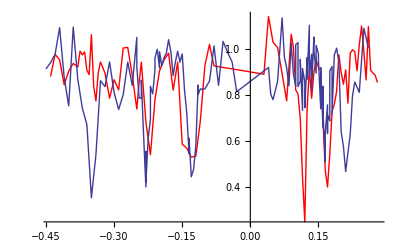

```mathematica
Show[ListLinePlot[J1vertdatasc,PlotStyle->Red],ListLinePlot[J1horizdatasc]]
```

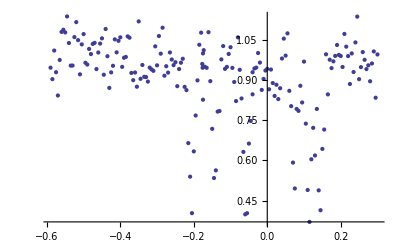

```mathematica
J1upperdata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\upperJ1data.txt","Data"],1];
J1upperdatasc=Table[{(J1upperdata[[i,2]]-59090)/100,J1upperdata[[i,1]]},{i,1,Length[J1upperdata]}];
ListPlot[J1upperdatasc,PlotRange->All]
```

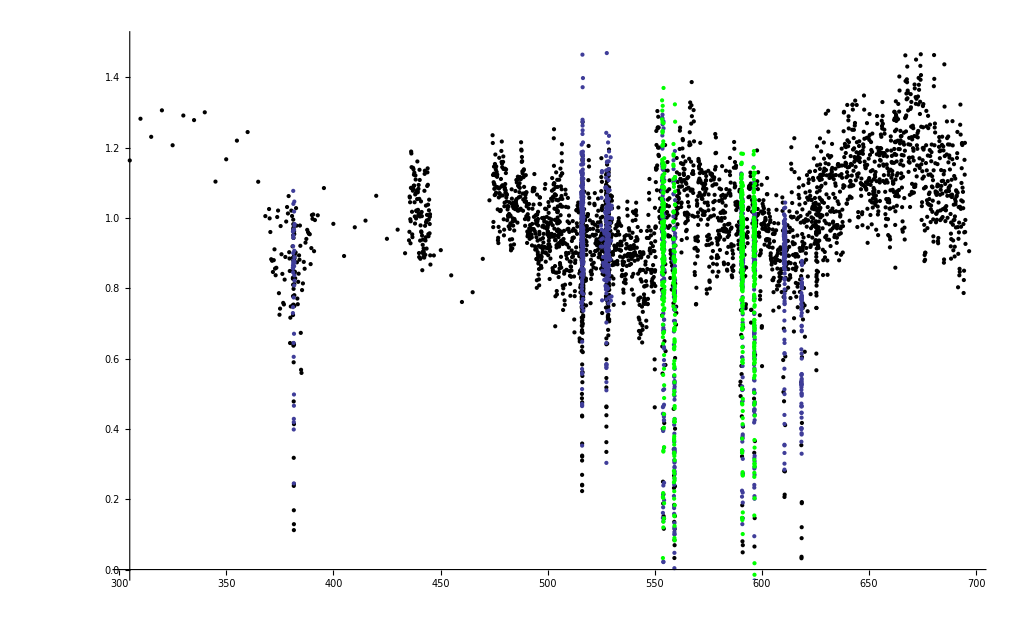

```mathematica
Broad804data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\BroadScan804nm.txt","Data"];
Detail804data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\DetailScan804nm.txt","Data"];
Detail804data372554=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_554THz_Norm.csv","Data"];
Detail804data372559=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_559THz_Norm.csv","Data"];
Detail804data372591=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_591THz_Norm.csv","Data"];
Detail804data372597=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_597THz_Norm.csv","Data"];
Show[ Show[ListPlot[Broad804data,PlotStyle->Black,PlotRange->{0,1.5}]],ListPlot[Detail804data],ListPlot[Detail804data372554,PlotStyle->Green],ListPlot[Detail804data372559,PlotStyle->Green],ListPlot[Detail804data372591,PlotStyle->Green],ListPlot[Detail804data372597,PlotStyle->Green],PlotRange->{0,1.5}]
```

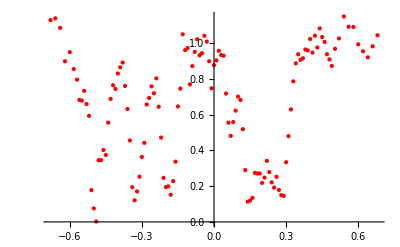

```mathematica
J1832data=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\c3J1832.txt","Data"],1];
J1832datasc=Table[{(J1832data[[i,1]]-190.7),J1832data[[i,2]]},{i,1,Length[J1832data]}];
Show[ListPlot[J1832datasc,PlotStyle->Red]]
```

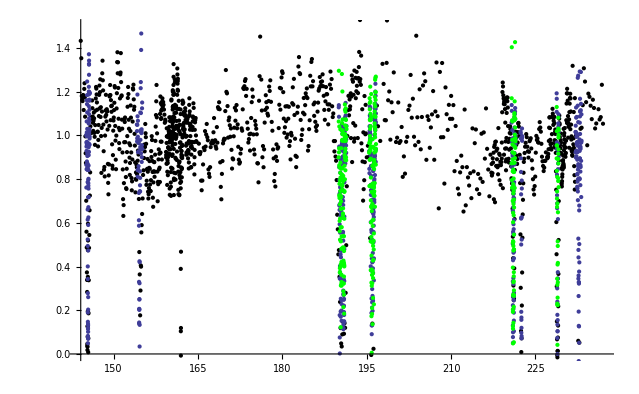

```mathematica
Detail832data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\Details360THzNormalized.csv","Data"];
Broad832data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\BroadScan360THzNormalized.csv","Data"];
Detail832data360191=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_191THz_Norm.csv","Data"];
Detail832data360195=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_195THz_Norm.csv","Data"];
Detail832data360221=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_221THz_Norm.csv","Data"];
Detail832data360229=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_229THz_Norm.csv","Data"];
Show[ Show[ListPlot[Broad832data,PlotStyle->Black,PlotRange->{0,1.5}]],ListPlot[Detail832data],ListPlot[Detail832data360191,PlotStyle->Green],ListPlot[Detail832data360195,PlotStyle->Green],ListPlot[Detail832data360221,PlotStyle->Green],ListPlot[Detail832data360229,PlotStyle->Green],PlotRange->{0,1.5}]
```

## Calculation

### Precalculated Parameters

```mathematica
(* 804 nm: *)
(*Bshift=-0.16;cshift=-0.4;bshift=3.1;λ=0.6;ξBc=0.6;ξbc=1.9;BL=BL0;γ=0;λb=0;
Bshift=-0.14;cshift=-0.33;bshift=3.67;λ=-0.56;ξBc=0.6;ξbc=0.63;γ=0;BL=0; (*804*)
Bshift=-0.09;cshift=-0.37;bshift=3.71;λ=-0.56;ξBc=0.58;ξbc=0.67;γ=0;BL=0; (*804*)
Bshift=-0.148;cshift=-0.32;bshift=3.67;λ=-0.54;ξBc=0.595;ξbc=0.67;γ=0;BL=0; (*804*)
Bshift=-0.143;cshift=-0.327;bshift=3.71;λ=-0.55;ξBc=0.590;ξbc=0.67;γ=0;BL=0; (*804*)
Bshift=-0.1283;cshift=-0.3399;bshift=3.71;λ=-0.55;ξBc=0.5899;ξbc=0.67;γ=0;BL=0;Nahf = 1.095;Khf = 1.3; (*804*)*)
ξBc=0.5899;ξbc=0.67;γ=0;BL=0;Nahf = 1.095;Khf = 1.3;
(* 832 nm: *)
(*Bshift=-0.1;cshift=1.47;bshift=-.21;λ=0.07;ξBc=0.158;ξbc=0.9;BL=BL0;γ=0;λb=0;
Bshift=-0.225;cshift=-0.01; bshift=0.1;λ=-0.19; ξBc = 0.35; ξbc=0.685; BL=0.0036; γ=0.004;
Bshift=-0.17;cshift=-0.065; bshift=0.095;λ=-0.23; ξBc = 0.28; ξbc=0.71; BL=0.0035; γ=0.01;
Bshift=-0.11;cshift=-0.125; bshift=0.1;λ=-0.275; ξBc = 0.158; ξbc=0.685; BL=0.0036; 
Bshift=-0.155;cshift=-0.08; bshift=0.095;λ=-0.23; ξBc = 0.25; ξbc=0.71; BL=0.0035; γ=0.004;*)
λb=0;
EJ01 =17699.3524;
EJ02= 17702.5023;
EJ11=17700.619602;
EJ12= 17701.847297;
Clear[Bshift,cshift,bshift,λ];
bshift[ξbc_]:=1/2 (EJ01+EJ02-√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2))-b3Pi+A;
Bshift[ξBc_,ξbc_]:=(EJ11+EJ12+√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξBc^2 ξbc^2)/(((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-B1Pi;
cshift[ξBc_,ξbc_]:=(EJ11+EJ12-√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξbc^2 (2 ξBc^2-(EJ11-EJ12)^2+(2(b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11-EJ12) √(-4 ξBc^2+(EJ11-EJ12)^2) ))/(2 ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)  ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-c3;
λ[ξBc_,ξbc_,γ_]:=(c3+cshift[ξBc,ξbc]-γ-1/2 (EJ01+EJ02+√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2)))/2
Bshift[ξBc,ξbc]
cshift[ξBc,ξbc]
bshift[ξbc]
λ[ξBc,ξbc,0]
```

-0.0725608

-0.260348

3.76949

-0.54553

### Final Hamiltonian:

```mathematica
Clear[Htotal]
Htotal[Bf_,Khf_,Khf2_]:=(B1Pi+Bshift[ξBc,ξbc]-BvB1Pi)H0B1Pi+BvB1Pi H0B1Pirot+Bf HZeemanB1Pi +(c3+cshift[ξBc,ξbc]-2Bvc3 -(-γ+2/3 λ[ξBc,ξbc,γ]))H0c3+Bvc3 H0c3rot+λ[ξBc,ξbc,γ] Hssc3+γ Hsrotc3+(b3Pi+bshift[ξbc]-Bvb3Pi)H0b3+Bvb3Pi Hrotb3+A HSOb3+λb Hssb3+ξBc HSOB1Pic3+ ξbc HSOb3Pic3+BL HJLb3Pic3+Bf HZeemanc3+Khf Hhyperfinec3+Khf2 Hhyperfinec3K;
Eigenvalues[Htotal[85.7,1.095 K1,1.3 K2][[4]]]
```

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.0557873,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,17701.4,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«4»+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.164673,-0.109782},{0.,0.,-0.109782,0.164673}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,-14.8122,0.},{0.,0.,0.,0.}}+«7» cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0.,0.,0.,0.},{0.,-0.363687,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,-0.00400567,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«1»+{{0.,0.,0.,0.},«2»,{0.,«3»}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,17714.4,0.},{0.,0.,0.,17714.4}}+{{0.,0.,0.,0.},{0.,0.,0.,0.67},{0.,0.,0.,0.},{0.,0.67,0.,0.}}+{{0.,0.,0.,0.},{0.,0.0796177,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«5» cannot be combined.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,17701.4,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,17701.4,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},«2»}+«9»+«7» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
maxTotalMF+1-9/2
```

3

```mathematica
Eigsystem=Table[{},{i,2 maxTotalMF+1}];
Eigvectors=Table[{},{i,2 maxTotalMF+1}];
JProjector=Table[{},{i,2 maxTotalMF+1}];
c3Proj=Table[{},{i,2 maxTotalMF+1}];
B1PiProj=Table[{},{i,2 maxTotalMF+1}];
b3Proj=Table[{},{i,2 maxTotalMF+1}];
LineStrengthv=Table[{},{i,2 maxTotalMF+1}];
LineStrengthh=Table[{},{i,2 maxTotalMF+1}];
GSLineStrength=Table[{},{i,2 maxTotalMF+1}];
For[iMF=1,iMF≤ 2maxTotalMF+1,
(*Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htotal[85.7,1.23K1,2.43K2][[iMF]]]]]];*)
Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htotal[85.7,1.15K1,1.15K2][[iMF]]]]]];
Eigvectors[[iMF]]=Transpose[Eigsystem[[iMF,All,2]]];
If[iMF≥3&&iMF≤6,
LineStrengthv[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixv[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];LineStrengthh[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixh[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];GSLineStrength[[iMF]]=Table[1(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].GSHoenlMatrixv[[iMF]].X00state)^2+0(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].GSHoenlMatrixh[[iMF]].X00state)^2,{i,1,nStates[[iMF]]}]];
(*JProjector[[iMF]]=Sum[J Chop[Eigvectors[[iMF]]ᵀ.Projector[iMF,J].Eigvectors[[iMF]]],{J,0,maxJ}];*)
c3Proj[[iMF]]= Chop[Eigvectors[[iMF]]ᵀ.c3Projector[iMF].Eigvectors[[iMF]],10^-3];
B1PiProj[[iMF]]= Chop[Eigvectors[[iMF]]ᵀ.B1PiProjector[iMF].Eigvectors[[iMF]],10^-3];
b3Proj[[iMF]]= Chop[Eigvectors[[iMF]]ᵀ.b3Projector[iMF].Eigvectors[[iMF]],10^-3];
iMF++];
```

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.0557873,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,17701.4,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«4»+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.164673,-0.109782},{0.,0.,-0.109782,0.164673}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,-14.8122,0.},{0.,0.,0.,0.}}+«7» cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0.,0.,0.,0.},{0.,-0.363687,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,-0.00400567,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«1»+{{0.,0.,0.,0.},«2»,{0.,«3»}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,17714.4,0.},{0.,0.,0.,17714.4}}+{{0.,0.,0.,0.},{0.,0.,0.,0.67},{0.,0.,0.,0.},{0.,0.67,0.,0.}}+{{0.,0.,0.,0.},{0.,0.0796177,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«5» cannot be combined.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,17701.4,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,17701.4,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},«2»}+«9»+«7» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 2 of Eigensystem[{}+{{-0.00200051,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0,0,0,0},{0,-0.363687,0,0},{0,0,0,0},{0,0,0,0}}+{{0,0,0,0},{0,-0.00400567,0,0},{0,0,0,0},{0,0,0,0}}+{{0,0,0,0},{0,0,0,0},{0,0,-14.8122,0},{0,0,0,0}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0,0,0,0},{0,0,0,0},{0,0,0.164673,-0.109782},{0,0,-0.109782,0.164673}}+{{0,0,0,0},{0,0,0,0},{0,0,17714.4,0},{0,0,0,17714.4}}+{{0,0,0,0},{0,0,0,0.67},{0,0,0,0},{0,0.67,0,0}}+{{0,0,0,0},{0,0.0796177,0,0},{0,0,0,0},{0,0,0,0}}+«5»] does not exist.

Part::partw: Part 2 of Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«2»},{0,-0.00200051,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},«2»}+«8»+«5»] does not exist.

Part::partw: Part 2 of Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«14»},{0,-0.00200051,0,0,0,0,0,0,0,0,«14»},{0,0,-0.00200051,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0.00200051,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},«14»}+«8»+«5»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 7 through 12 in ….

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
(Eigsystem[[3,All,1]]-DeX)100 c 10^-9-FB0-372000
Table[Eigvectors[[3,7,i]]/Eigvectors[[3,13,i]],{i,1,nStates[[3]]}]
Table[Eigvectors[[3,8,i]]/Eigvectors[[3,14,i]],{i,1,nStates[[3]]}]
```

{530.492,530.492,530.492,530.492,530.492,530.492,555.828,555.954,556.04,556.186,556.246,556.304,592.742,592.81,592.885,592.932,592.982,593.029,975.597,975.597,975.597,975.598,975.598,975.598}

{-0.00462939,-0.00460072,-0.00458526,-0.00454832,-0.00453735,-0.00452658,160.49,161.243,161.75,162.622,162.976,163.321,359.572,359.904,360.265,360.492,360.732,360.96,-6.70881,-6.71214,-6.71384,-6.71838,-6.71963,-6.72087}

{-0.00462937,-0.00460076,-0.00458528,-0.00454832,-0.00453734,-0.00452656,160.49,161.243,161.75,162.622,162.976,163.321,359.572,359.904,360.265,360.492,360.732,360.96,-6.70881,-6.71214,-6.71384,-6.71838,-6.71963,-6.72087}

```mathematica
(Eigsystem[[3,All,1]]-DeX)100 c 10^-9-FB0-372000
(Eigsystem[[5,All,1]]-DeX)100 c 10^-9-FB0-372000
```

{528.709,528.709,528.709,528.709,528.709,528.709,553.766,553.893,553.978,554.125,554.185,554.243,590.692,590.76,590.835,590.882,590.931,590.979,973.813,973.813,973.813,973.814,973.814,973.814}

{528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,553.707,553.772,553.901,553.974,553.989,553.997,554.138,554.189,554.241,554.29,554.336,590.654,590.697,590.765,590.832,590.838,590.84,590.89,590.934,590.976,591.014,591.047,973.812,973.813,973.813,973.813,973.813,973.813,973.814,973.814,973.814,973.814,973.815}

The simple ratio of widths does not give us the correct admixture. This is only true to a first approximation.

```mathematica
554.336-553.766
591.047-590.692
(554.336-553.766)/(591.047-590.692)
```

0.57

0.355

1.60563

Let’s look for the ratio of triplet-Sigma to singlet-Pi:

```mathematica
(Eigsystem[[5,All,1]]-DeX)100 c 10^-9-FB0-372000
Table[c3Proj[[5,i,i]],{i,1,nStates[[3]]}]
Table[B1PiProj[[5,i,i]],{i,1,nStates[[3]]}]
Table[c3Proj[[5,i,i]]/(B1PiProj[[5,i,i]]+0.0000001),{i,1,nStates[[3]]}]
```

{528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,528.709,553.707,553.772,553.901,553.974,553.989,553.997,554.138,554.189,554.241,554.29,554.336,590.654,590.697,590.765,590.832,590.838,590.84,590.89,590.934,590.976,591.014,591.047,973.812,973.813,973.813,973.813,973.813,973.813,973.814,973.814,973.814,973.814,973.815}

{0,0,0,0,0,0,0,0,0,0,0,0.644999,0.644114,0.641506,0.641132,0.640759,0.640545,0.636446,0.636063,0.635625,0.635102,0.634533,0.352637,0.35369}

{0,0,0,0,0,0,0,0,0,0,0,0.353497,0.354384,0.356997,0.357372,0.357745,0.35796,0.362067,0.362451,0.36289,0.363414,0.363984,0.646387,0.645331}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82462,1.81756,1.79695,1.79402,1.79111,1.78943,1.75781,1.75489,1.75156,1.7476,1.7433,0.545552,0.548075}

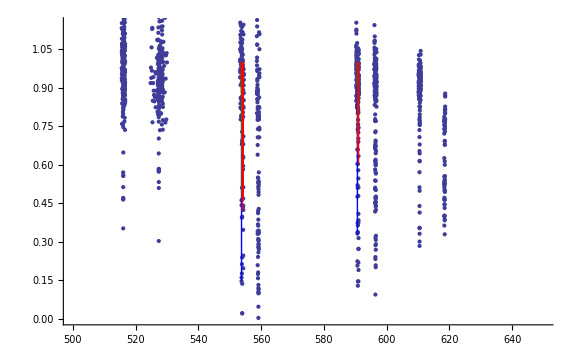

```mathematica
Show[ListPlot[Detail804data],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000),Exp[-60 LineStrengthh[[iMF,i]]-60 LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],PlotRange->{{500,650},{0,1.15}},ImageSize->Large]
```

### lower J=1: 372.554 THz

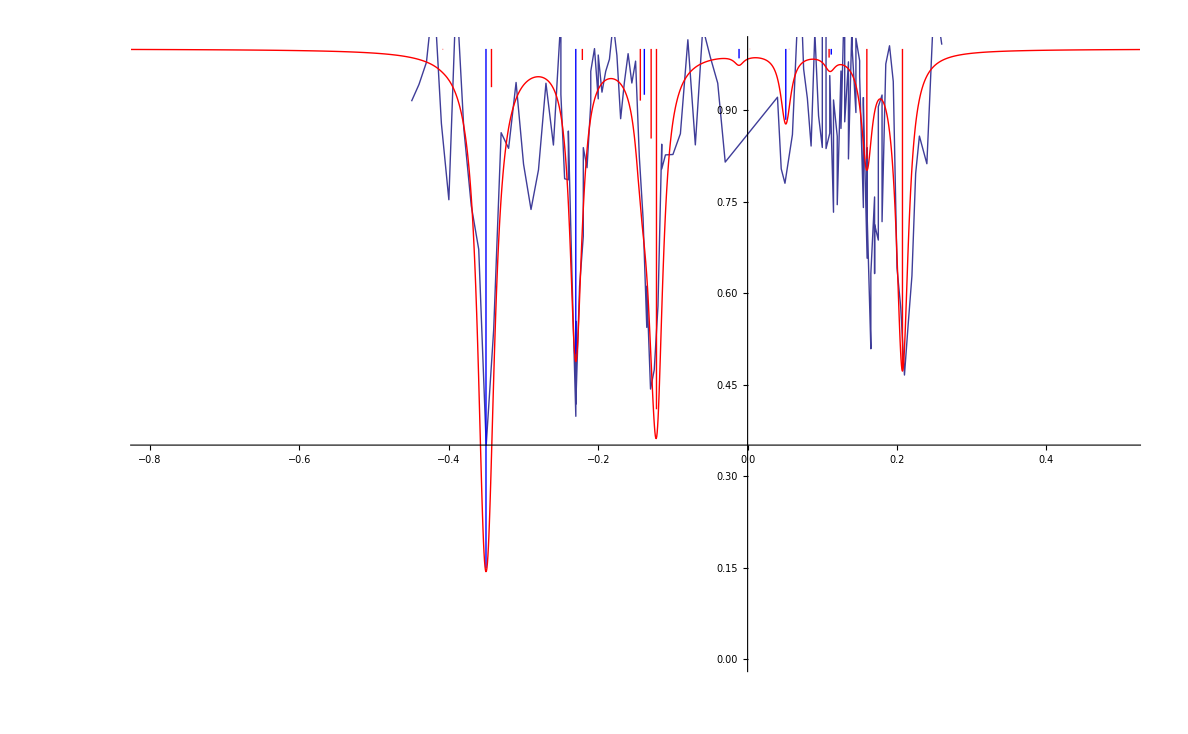

```mathematica
Module[{Offs=.42},Show[ListLinePlot[J1horizdatasc],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{(Eigsystem[[iMF,i,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs),Exp[-60 LineStrengthh[[iMF,i]]-0 60LineStrengthv[[iMF,i]]]},{(Eigsystem[[iMF,i,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
Plot[Exp[-60*Sum[Sum[1/(1+(x-(Eigsystem[[iiMF,ii,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs))^2/0.008^2)*(LineStrengthh[[iiMF,ii]]+0LineStrengthv[[iiMF,ii]]),{ii,1,nStates[[iiMF]]}],{iiMF,-9/2+maxTotalMF+1,-5/2+maxTotalMF+1,1}]],{x,-1,1},PlotStyle->Red,PlotRange->All],PlotRange->{{-.8,.5},{0,1}}]]
```

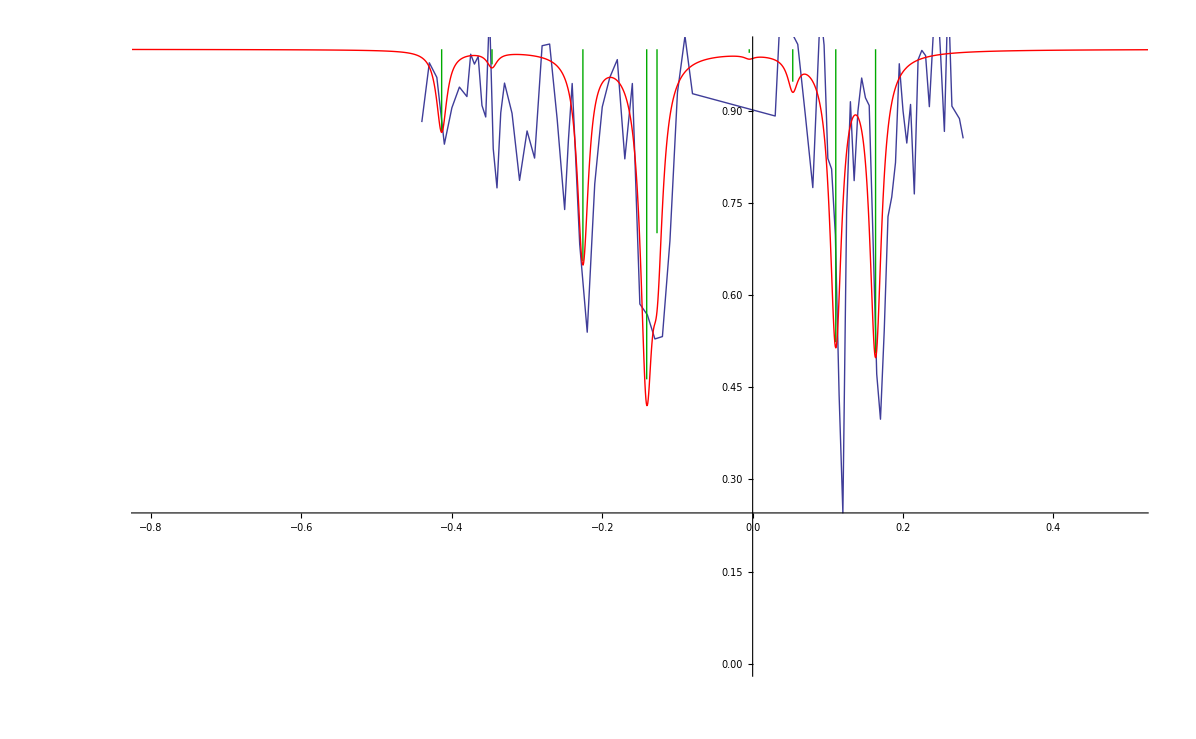

```mathematica
Module[{Offs=.42},Show[ListLinePlot[J1vertdatasc],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{(Eigsystem[[iMF,i,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs),Exp[-60 0 LineStrengthh[[iMF,i]]-1 60LineStrengthv[[iMF,i]]]},{(Eigsystem[[iMF,i,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
Plot[Exp[-60*Sum[Sum[1/(1+(x-(Eigsystem[[iiMF,ii,1]]100 c 10^-9-5.306 10^5-51.0-0.7+Offs))^2/0.008^2)*(0LineStrengthh[[iiMF,ii]]+1LineStrengthv[[iiMF,ii]]),{ii,1,nStates[[iiMF]]}],{iiMF,-9/2+maxTotalMF+1,-5/2+maxTotalMF+1,1}]],{x,-1,1},PlotStyle->Red,PlotRange->All],PlotRange->{{-.8,.5},{0,1}}]]
```

```mathematica
bshift[ξbc]
```

3.76949

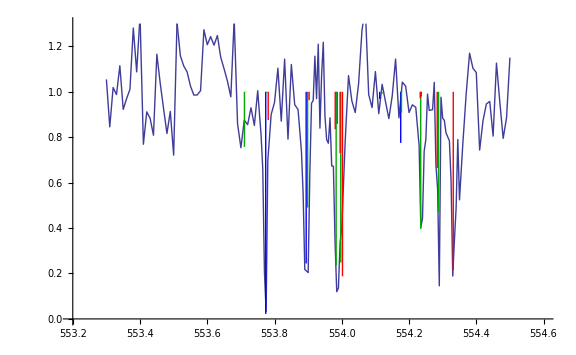

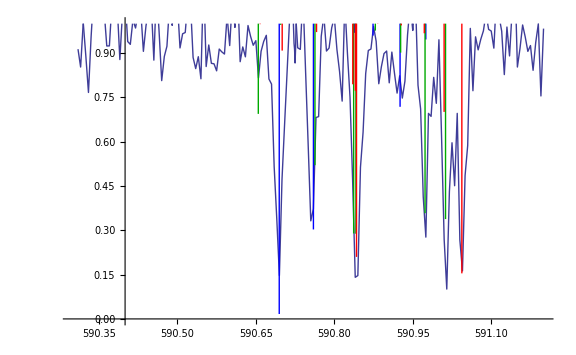

```mathematica
For[iMF=3,iMF≤5,
(*Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htotal[85.7,1.23K1,2.43K2][[iMF]]]]]];*)
ξbc=.767;
BL=0.000;
γ=0;
Bf=85.7;
Htot=(B1Pi+Bshift[ξBc,ξbc]-BvB1Pi)H0B1Pi+BvB1Pi H0B1Pirot+Bf HZeemanB1Pi +(c3+cshift[ξBc,ξbc]-2Bvc3 -(-γ+2/3 λ[ξBc,ξbc,γ]))H0c3+Bvc3 H0c3rot+λ[ξBc,ξbc,γ] Hssc3+γ Hsrotc3+(b3Pi+bshift[ξbc]-Bvb3Pi)H0b3+Bvb3Pi Hrotb3+A HSOb3+λb Hssb3+ξBc HSOB1Pic3+ ξbc HSOb3Pic3+BL HJLb3Pic3+Bf HZeemanc3+Nahf K1 Hhyperfinec3+Khf K2 Hhyperfinec3K;
Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htot[[iMF]]]]]];
Eigvectors[[iMF]]=Transpose[Eigsystem[[iMF,All,2]]];
If[iMF≥3&&iMF≤6,
LineStrengthv[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixv[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];LineStrengthh[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixh[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}]];
iMF++];
Offs=0;
Show[ListLinePlot[Detail804data372554,PlotRange->{{553.2,554.6},{0,1.3}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-120 LineStrengthh[[iMF,i]]-120LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
PlotRange->{{553.2,554.6},{0,1.3}},ImageSize->Large]
Show[ListLinePlot[Detail804data372591,PlotRange->{{590.3,591.2},{0,1}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-220 LineStrengthh[[iMF,i]]-220LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],PlotRange->{{590.3,591.2},{0,1}},ImageSize->Large]
```

```mathematica
Restab={};
Offs=0;
For[iMF=-9/2+maxTotalMF+1,iMF≤-5/2+maxTotalMF+1,
For[i=1,i≤nStates[[iMF]],
If[((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs)>553.2&&((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs)<554.6,
AppendTo[Restab,{804,1,2(iMF-1-maxTotalMF),i,((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Offs,LineStrengthh[[iMF,i]],LineStrengthv[[iMF,i]],120,0,0.005}]];
i++];
iMF++];
Offs=0;
For[iMF=-9/2+maxTotalMF+1,iMF≤-5/2+maxTotalMF+1,
For[i=1,i≤nStates[[iMF]],
If[((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs)>590&&((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs)<591.4,
AppendTo[Restab,{804,1,2(iMF-1-maxTotalMF),i,((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Offs,LineStrengthh[[iMF,i]],LineStrengthv[[iMF,i]],200,0,0.005}]];
i++];
iMF++];
```

```mathematica
Export["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\Singlet STIRAP\\Results804J1.dat",Restab];
```

```mathematica
Manipulate[For[iMF=3,iMF≤5,
(*Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htotal[85.7,1.23K1,2.43K2][[iMF]]]]]];*)
ξbc=0.67;γ=0;BL=0; (*804*)
Bf=85.7;
Htot=(B1Pi+Bshift[ξBc,ξbc]-BvB1Pi)H0B1Pi+BvB1Pi H0B1Pirot+Bf HZeemanB1Pi +(c3+cshift[ξBc,ξbc]-2Bvc3 -(-γ+2/3 λ[ξBc,ξbc,γ]))H0c3+Bvc3 H0c3rot+λ[ξBc,ξbc,γ] Hssc3+γ Hsrotc3+(b3Pi+bshift[ξbc]-Bvb3Pi)H0b3+Bvb3Pi Hrotb3+A HSOb3+λb Hssb3+ξBc HSOB1Pic3+ ξbc HSOb3Pic3+BL HJLb3Pic3+Bf HZeemanc3+Nahf K1 Hhyperfinec3+Khf K2 Hhyperfinec3K;
Eigsystem[[iMF]]=Sort[Transpose[Chop[Eigensystem[Htot[[iMF]]]]]];
Eigvectors[[iMF]]=Transpose[Eigsystem[[iMF,All,2]]];
If[iMF≥3&&iMF≤6,
LineStrengthv[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixv[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];LineStrengthh[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixh[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}]];
iMF++];
Offs=0;
Show[ListLinePlot[Detail804data372554,PlotRange->{{553.2,554.6},{0,1.3}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-120 LineStrengthh[[iMF,i]]-120LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
PlotRange->{{553.2,554.6},{0,1.3}},ImageSize->Large]
Show[ListLinePlot[Detail804data372591,PlotRange->{{590.3,591.2},{0,1.3}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-120 LineStrengthh[[iMF,i]]-120LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],PlotRange->{{590.3,591.2},{0,1.3}},ImageSize->Large],{ξBc,0,1,Appearance->"Labeled"},{Nahf,0,2,Appearance->"Labeled"},{Khf,0,2,Appearance->"Labeled"}]
```

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::noval: Symbol Eigsystem in part assignment does not have an immediate value.

Part::partd: Part specification Eigsystem⟦3,All,2⟧ is longer than depth of object.

Set::noval: Symbol Eigvectors in part assignment does not have an immediate value.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

Set::noval: Symbol LineStrengthv in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Part::partd: Part specification nStates⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStates⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372591,PlotRange→{{590.3,591.2},{0,1.3}}],{,,},PlotRange→{{590.3,591.2},{0,1.3}},ImageSize→Large].

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Detail804data372554,PlotRange→{{553.2,554.6},{0,1.3}}],{,,},PlotRange→{{553.2,554.6},{0,1.3}},ImageSize→Large].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.0557873,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,17701.4,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«4»+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.164673,-0.109782},{0.,0.,-0.109782,0.164673}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,-14.8122,0.},{0.,0.,0.,0.}}+«7» cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0.,0.,0.,0.},{0.,-0.363687,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,-0.00400567,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«1»+{{0.,0.,0.,0.},«2»,{0.,«3»}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,17714.4,0.},{0.,0.,0.,17714.4}}+{{0.,0.,0.,0.},{0.,0.,0.,0.67},{0.,0.,0.,0.},{0.,0.67,0.,0.}}+{{0.,0.,0.,0.},{0.,0.0796177,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«5» cannot be combined.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,17701.4,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,17701.4,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},«2»}+«9»+«7» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 2 of Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«14»},{0,-0.00200051,0,0,0,0,0,0,0,0,«14»},{0,0,-0.00200051,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0.00200051,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},«14»}+«8»+«5»] does not exist.

Part::take: Cannot take positions 7 through 12 in ….

Part::partw: Part 2 of Transpose[Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«14»},{0,-0.00200051,0,0,0,0,0,0,0,0,«14»},{0,0,-0.00200051,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0.00200051,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},«14»}+«8»+«5»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 7 through 12 in ….

General::stop: Further output of Part::take will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[<<2480298112 bytes>>].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[<<2480298112 bytes>>].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.0557873,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,17701.4,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«4»+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.164673,-0.109782},{0.,0.,-0.109782,0.164673}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,-14.8122,0.},{0.,0.,0.,0.}}+«7» cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{{-0.00200051,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{0.,0.,0.,0.},{0.,-0.363687,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+{{0.,0.,0.,0.},{0.,-0.00400567,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«1»+{{0.,0.,0.,0.},«2»,{0.,«3»}}+{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,17714.4,0.},{0.,0.,0.,17714.4}}+{{0.,0.,0.,0.},{0.,0.,0.,0.67},{0.,0.,0.,0.},{0.,0.67,0.,0.}}+{{0.,0.,0.,0.},{0.,0.0796177,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}+«5» cannot be combined.

Thread::tdlen: Objects of unequal length in {{17701.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,17701.4,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,17701.4,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2»},«2»}+«9»+«7» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 2 of Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«14»},{0,-0.00200051,0,0,0,0,0,0,0,0,«14»},{0,0,-0.00200051,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0.00200051,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},«14»}+«8»+«5»] does not exist.

Part::take: Cannot take positions 7 through 12 in ….

Part::partw: Part 2 of Transpose[Eigensystem[{}+{{-0.00200051,0,0,0,0,0,0,0,0,0,«14»},{0,-0.00200051,0,0,0,0,0,0,0,0,«14»},{0,0,-0.00200051,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0.00200051,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},{0,0,0,0,0,0,0,0,0,0,«14»},«14»}+«8»+«5»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 7 through 12 in ….

General::stop: Further output of Part::take will be suppressed during this calculation.

ListLinePlot::lpn: Detail804data372554 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[<<2480298112 bytes>>].

ListLinePlot::lpn: Detail804data372591 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[<<2480298112 bytes>>].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

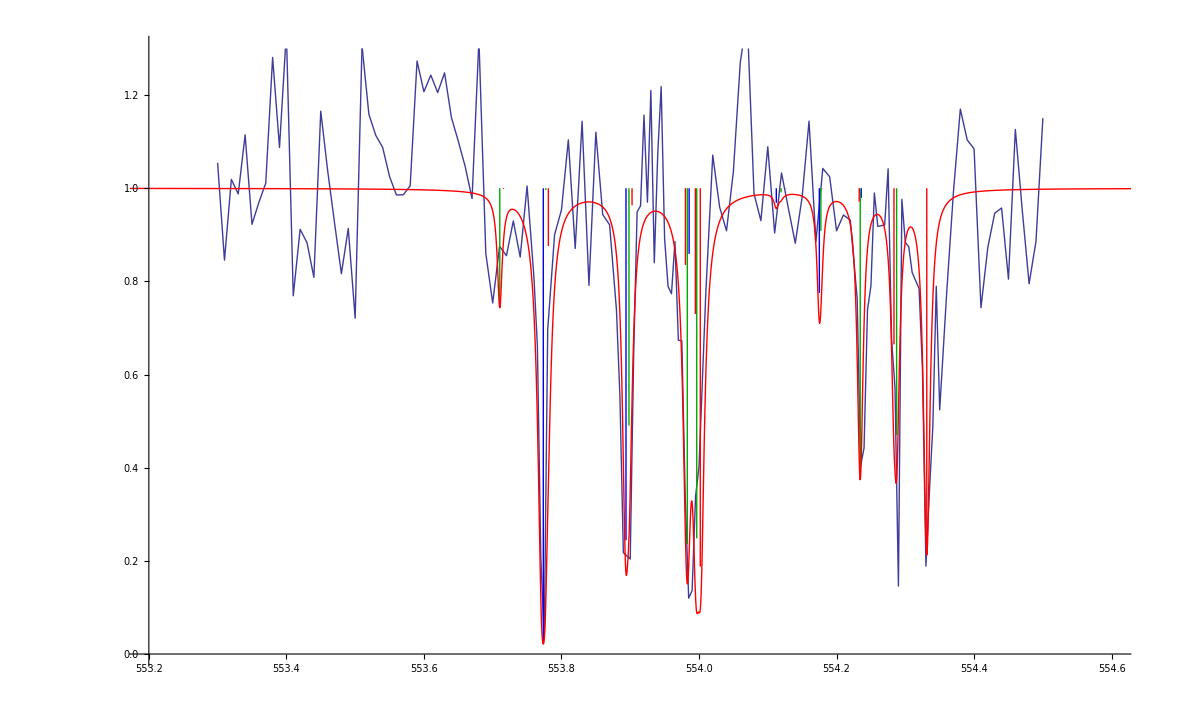

```mathematica
Module[{Offs=0},
Show[ListLinePlot[Detail804data372554,PlotRange->{{553.2,554.6},{0,1.3}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-120 LineStrengthh[[iMF,i]]-120LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
Plot[Exp[-120*Sum[Sum[1/(1+(x-((Eigsystem[[iiMF,ii,1]]-DeX)100 c 10^-9-FB0-372000+Offs))^2/0.004^2)*( LineStrengthh[[iiMF,ii]]+LineStrengthv[[iiMF,ii]]),{ii,1,nStates[[iiMF]]}],{iiMF,-9/2+maxTotalMF+1,-5/2+maxTotalMF+1,1}]],{x,553,555},PlotStyle->Red,PlotRange->All],PlotRange->{{553.2,554.6},{0,1.3}}]]
```

### upper J=1: 372.591 THz

```mathematica
FBStatecback={-0.08431320687534541,0.20935326118536976,0.08955936893360888,0.25224725117942387,-0.09882714587886539,-0.19967658195534696,-0.7144810441063647,0.35381338575191507,0.43830163405763906};
```

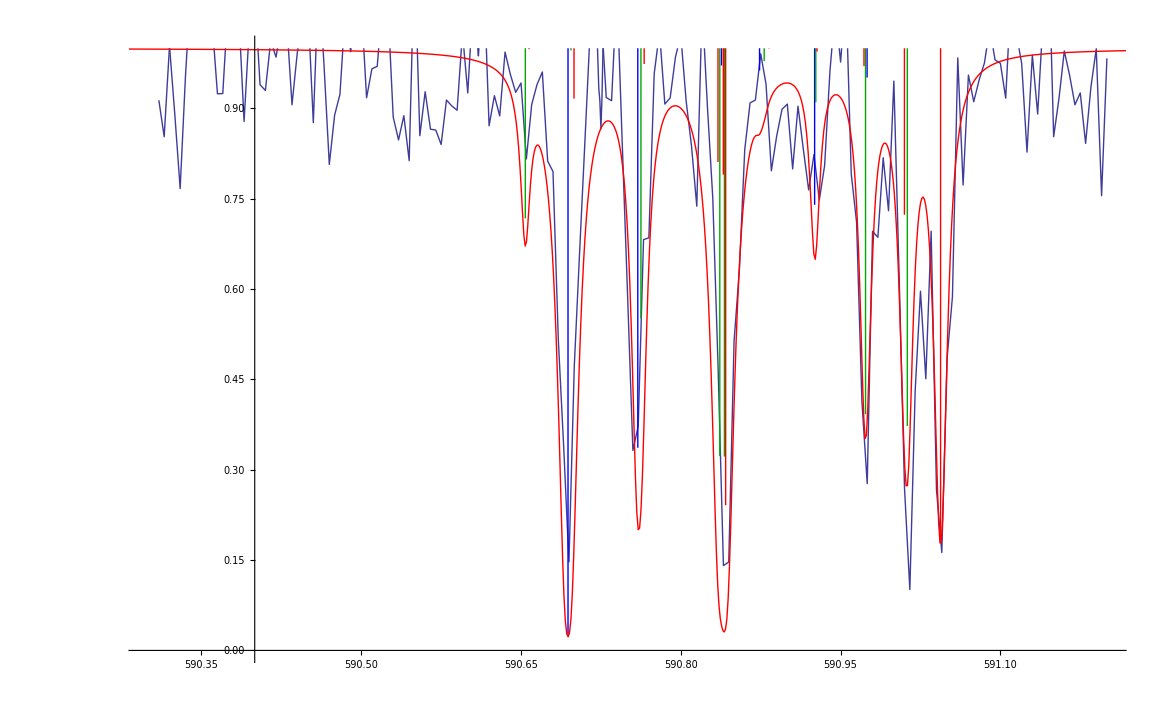

```mathematica
Module[{Offs=0},
(*FBStatec=√α WeightedABMQstates+√(1-α)PChannelABM /.α->.99;FBStatec=FBStatec/(√(FBStatec.FBStatec));*)
For[iMF=3,iMF≤5,
LineStrengthv[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixv[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];LineStrengthh[[iMF]]=Table[(Eigsystem[[iMF,i,2]][[Length[B1basis[[iMF]]]+1;;Length[B1basis[[iMF]]]+Length[c3basis[[iMF]]]]].HoenlMatrixh[[iMF]].FBStatec)^2,{i,1,nStates[[iMF]]}];
iMF++];
Show[ListLinePlot[Detail804data372591,PlotRange->{{590.3,591.2},{0,1}}],Table[Graphics[Table[{Directive[Thick,Switch[iMF,3,Blue,4,Darker[Green],5,Red]],Line[{{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),Exp[-200 LineStrengthh[[iMF,i]]-200LineStrengthv[[iMF,i]]]},{((Eigsystem[[iMF,i,1]]-DeX)100 c 10^-9-FB0-372000+Offs),1}}]},{i,1,nStates[[iMF]]}]],{iMF,3,5,1}],
Plot[Exp[-200*Sum[Sum[1/(1+(x-((Eigsystem[[iiMF,ii,1]]-DeX)100 c 10^-9-FB0-372000+Offs))^2/0.005^2)*( LineStrengthh[[iiMF,ii]]+LineStrengthv[[iiMF,ii]]),{ii,1,nStates[[iiMF]]}],{iiMF,-9/2+maxTotalMF+1,-5/2+maxTotalMF+1,1}]],{x,588,592},PlotStyle->Red,PlotRange->All],PlotRange->{{590.3,591.2},{0,1}}]]
```